## Úloha 2

V druhé úloze se podíváme, jak se chová norma || f - p_n || a norma derivací ||(d f)/dx-(d p_n)/dx||, kde p_n je interpolační polynom získaný Chebyshevovou interpolací,  v závislosti na n.
Body, ve kterých budeme interpolovat (kořeny Chebyshevova polynomu), jsou dány vztahem:

```mathematica
nmax=30;
koreny = N[Table[NumericalSort[Table[Cos[Pi*(2*k-1)/(2*n)], {k,1,n}]],{n,1,nmax}]];
```

kde n je stupeň polynomu.

### Funkce spojitá se spojitými derivacemi

Zvolme si například funkci

```mathematica
f1[x_]:=Exp[1/(1+x^2)];
```

Poté interpolace je tvaru

```mathematica
pn1=Table[InterpolatingPolynomial[Table[{koreny[[n]][[k]],f1[koreny[[n]][[k]]]},{k,1,n}],x],{n,1,nmax}];
obr1=Table[Show[Plot[pn1[[n]],{x,-1,1}],Plot[f1[x],{x,-1,1}], PlotRange->All],{n,1,nmax}];
```

```mathematica
Manipulate[obr1[[n]],{n,1,nmax,1},SaveDefinitions->True]
```

Nyní se podívejme na dvojkovou normu rozdílu puvodní a interpolované funkce

{0.859489,0.628308,0.166344,0.140129,0.0356369,0.0315276,0.00790146,0.0070029,0.00173244,0.00153347,0.000375091,0.000331712,0.0000803413,0.0000710073,0.0000170498,0.0000150625,3.58909×10^-6,3.16972×10^-6,7.50127×10^-7,6.62304×10^-7,1.55775×10^-7,1.37508×10^-7,3.21621×10^-8,2.83853×10^-8,6.60548×10^-9,5.82889×10^-9,1.35013×10^-9,1.19123×10^-9,2.7474×10^-10,2.42377×10^-10}

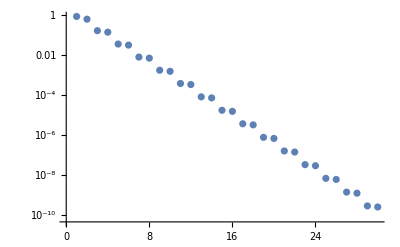

```mathematica
norm2f1=Table[Sqrt[NIntegrate[(f1[x]-pn1[[n]])^2,{x,-1,1}]],{n,1,nmax}]
ListLogPlot[norm2f1]
```

Nyní se podívejme na maximovou normu rozdílu puvodní a interpolované funkce

{2.3504,1.57985,0.193755,0.185726,0.0444989,0.0418812,0.00974106,0.0092682,0.00216196,0.00202271,0.000465205,0.000436311,0.000100338,0.0000931733,0.0000214629,0.0000197231,4.53246×10^-6,4.14282×10^-6,9.45013×10^-7,7.68162×10^-7,1.97101×10^-7,1.79162×10^-7,4.07492×10^-8,3.69346×10^-8,8.36631×10^-9,7.05714×10^-9,1.71424×10^-9,1.5464×10^-9,3.48999×10^-10,3.1432×10^-10}

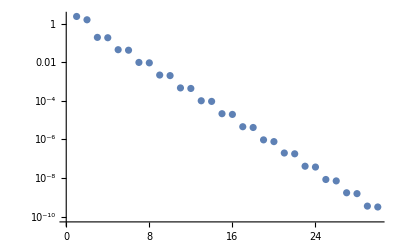

```mathematica
normmf1=Table[Abs[MaxValue[{Simplify[f1[x]-pn1[[n]]],-1<=x<=1},x]],{n,1,nmax}]
ListLogPlot[normmf1]
```

Podívejme se na derivaci původní a interpolované funkce, vykresleme si je podívejme se na normu (dvojkovou a maximovou).

{1.59015,1.59015,0.998274,0.765926,0.397362,0.267783,0.129502,0.0811698,0.0377585,0.0226291,0.01026,0.00596392,0.00265414,0.00150879,0.000661897,0.000369893,0.000160412,0.0000884368,0.0000379889,0.0000207131,8.82613×10^-6,4.76809×10^-6,2.01771×10^-6,1.0815×10^-6,4.54895×10^-7,2.4218×10^-7,1.01322×10^-7,5.36249×10^-8,2.23287×10^-8,1.17561×10^-8}

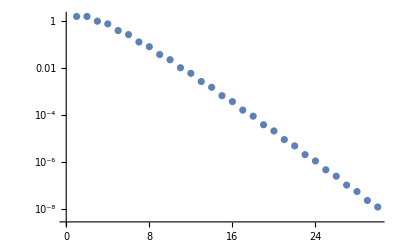

{(2 √(1/3 (-2+√7)) ⅇ^(1/(1+1/3 (-2+√7))))/(1+1/3 (-2+√7))^2,(2 √(1/3 (-2+√7)) ⅇ^(1/(1+1/3 (-2+√7))))/(1+1/3 (-2+√7))^2,1.70227,1.09093,1.08209,0.589214,0.475495,0.238628,0.173164,0.0828757,0.056212,0.0260877,0.0168686,0.00766251,0.00477886,0.000492735,0.00129518,0.000572234,0.000338845,0.000148305,0.0000861215,0.0000374095,2.81232×10^-6,9.22346×10^-6,5.19242×10^-6,2.23004×10^-6,1.23965×10^-6,5.301×10^-7,2.91395×10^-7,1.24146×10^-7}

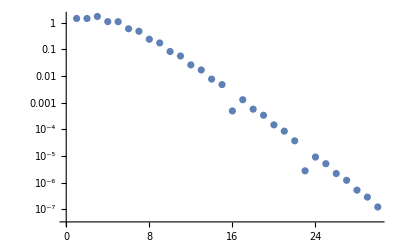

```mathematica
dobr1=Table[Show[Plot[Evaluate[D[pn1[[n]],x]],{x,-1,1}],Plot[f1'[x],{x,-1,1}], PlotRange->All],{n,1,nmax}];
Manipulate[dobr1[[n]],{n,1,nmax,1},SaveDefinitions->True]
norm2d1=Table[Sqrt[NIntegrate[(f1'[x]-D[pn1[[n]],x])^2,{x,-1,1}]],{n,1,nmax}]
ListLogPlot[norm2d1]
normmd1=Table[Abs[MaxValue[{Simplify[f1'[x]-D[pn1[[n]],x]],-1<=x<=1},x]],{n,1,nmax}]
ListLogPlot[normmd1]
```

### Funkce po částech spojitá s po částech spojitými derivacemi

Zvolme si například funkci

```mathematica
f2[x_]=Piecewise[{{Exp[x], x>=0}, {1/-Exp[x], x<0}}];
```

Interpolace

```mathematica
pn2=Table[InterpolatingPolynomial[Table[{koreny[[n]][[k]],f2[koreny[[n]][[k]]]},{k,1,n}],x],{n,1,nmax}];
obr2=Table[Show[Plot[pn2[[n]],{x,-1,1}],Plot[f2[x],{x,-1,1}], PlotRange->All],{n,1,nmax}];
```

```mathematica
Manipulate[obr2[[n]],{n,1,nmax,1},SaveDefinitions->True]
```

Norma

{2.89639,0.632961,1.16861,0.531212,0.954241,0.449112,0.812662,0.395716,0.719537,0.357526,0.652393,0.232311,0.120584,0.216083,0.113439,0.202828,0.107428,0.19174,0.102278,0.182288,0.0978027,0.174106,0.0938663,0.166933,0.090369,0.160579,0.0872347,0.154898,0.084405,0.14978}

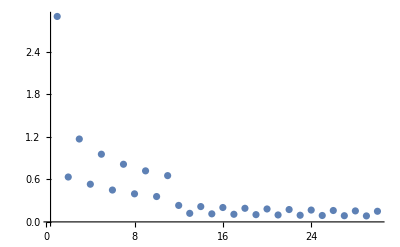

{Abs[MaxValue[{Piecewise[{{ⅇ^-x, x<0}, {ⅇ^x, x>0}, {Indeterminate, True}}],-1≤x≤1},x]],0.149906,2.63971,3.34537,6.07371,1.81333,5.46484,7.59576,10.3482,2.41344,9.41432,11.7204,14.4388,3.20449,13.4042,15.7874,18.4794,4.03454,17.4028,19.8288,22.5017,4.87983,21.4037,23.8568,26.5156,5.73278,25.4052,27.877,30.525,6.39151}

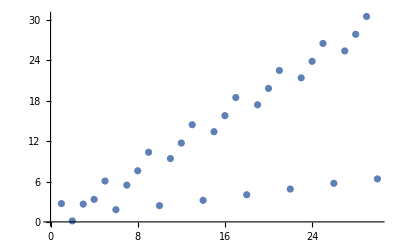

```mathematica
norm2f2=Table[Sqrt[NIntegrate[(f2[x]-pn2[[n]])^2,{x,-1,1}]],{n,1,nmax}]
ListPlot[norm2f2,PlotRange->All]
normmf2=Table[Abs[MaxValue[{Simplify[f2'[x]-D[pn2[[n]],x]],-1<=x<=1},x]],{n,1,nmax}]
ListPlot[normmf2]
```

Derivace

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.0215445}. NIntegrate obtained 23.5843 and 0.00516378 for the integral and error estimates.

{2.52766,1.7688,2.70815,2.8868,3.3893,3.5471,3.91728,4.0747,4.37166,4.52557,4.778,4.85637,2.04838,3.74282,2.18601,3.98268,2.31209,4.20736,2.42908,4.41953,2.53872,4.62117,2.64227,4.81374,2.74068,4.99842,2.83467,5.17612,2.92481,5.3476}

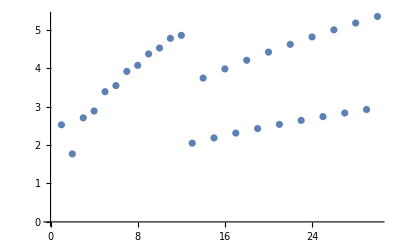

{Abs[MaxValue[{Piecewise[{{ⅇ^-x, x<0}, {ⅇ^x, x>0}, {Indeterminate, True}}],-1≤x≤1},x]],0.149906,2.63971,3.34537,6.07371,1.81333,5.46484,7.59576,10.3482,2.41344,9.41432,11.7204,14.4388,3.20449,13.4042,15.7874,18.4794,4.03454,17.4028,19.8288,22.5017,4.87983,21.4037,23.8568,26.5156,5.73278,25.4052,27.877,30.525,6.39151}

-Graphics-

```mathematica
dobr2=Table[Show[Plot[Evaluate[D[pn2[[n]],x]],{x,-1,1}],Plot[f2'[x],{x,-1,1}], PlotRange->All],{n,1,nmax}];
Manipulate[dobr2[[n]],{n,1,nmax,1},SaveDefinitions->True]
norm2d2=Table[Sqrt[NIntegrate[(f2'[x]-D[pn2[[n]],x])^2,{x,-1,1}]],{n,1,nmax}]
ListPlot[norm2d2]
normmd2=Table[Abs[MaxValue[{Simplify[f2'[x]-D[pn2[[n]],x]],-1<=x<=1},x]],{n,1,nmax}]
ListPlot[normmd2]
```

### Funkce oscilující

Zvolme si například funkci

```mathematica
f3[x_]=Cos[10*Sin[x]];
```

Interpolace

```mathematica
pn3=Table[InterpolatingPolynomial[Table[{koreny[[n]][[k]],f3[koreny[[n]][[k]]]},{k,1,n}],x],{n,1,nmax}];
obr3=Table[Show[Plot[pn3[[n]],{x,-1,1}],Plot[f3[x],{x,-1,1}], PlotRange->All],{n,1,nmax}];
```

```mathematica
Manipulate[obr3[[n]],{n,1,nmax,1},SaveDefinitions->True]
```

Norma

{1.5581,1.53271,1.3421,1.44433,1.37888,1.21278,0.98335,0.902534,0.498003,0.449153,0.18157,0.162,0.0520646,0.0461636,0.0124229,0.0109708,0.00255804,0.00225278,0.000466131,0.000409671,0.0000765498,0.0000671736,0.000011487,0.0000100677,1.59208×10^-6,1.394×10^-6,2.0557×10^-7,1.79847×10^-7,2.49025×10^-8,2.17716×10^-8}

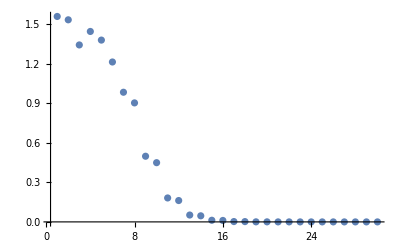

{-10 Cos[Root6.13Root[{10 Cos[10 Sin[#1]] Cos[#1]^2-Sin[10 Sin[#1]] Sin[#1]&,6.1270655027312168001}]6.127065502731217] Sin[10 Sin[Root6.13Root[{10 Cos[10 Sin[#1]] Cos[#1]^2-Sin[10 Sin[#1]] Sin[#1]&,6.1270655027312168001}]6.127065502731217]],-10 Cos[Root6.13Root[{10 Cos[10 Sin[#1]] Cos[#1]^2-Sin[10 Sin[#1]] Sin[#1]&,6.1270655027312168001}]6.127065502731217] Sin[10 Sin[Root6.13Root[{10 Cos[10 Sin[#1]] Cos[#1]^2-Sin[10 Sin[#1]] Sin[#1]&,6.1270655027312168001}]6.127065502731217]],9.82725,10.1902,9.71816,12.664,29.5418,11.4958,36.8283,12.9139,23.5842,9.5772,10.3305,4.45567,3.47557,0.357988,0.956944,0.43438,0.224426,0.103179,0.0460794,0.021376,0.00109593,0.00394593,0.00140491,0.000659418,0.000214306,0.000100993,0.0000302763,0.0000143146}

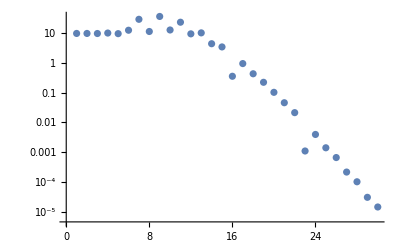

```mathematica
norm2f3=Table[Sqrt[NIntegrate[(f3[x]-pn3[[n]])^2,{x,-1,1}]],{n,1,nmax}]
ListPlot[norm2f3,PlotRange->All]
normmf3=Table[Abs[MaxValue[{Simplify[f3'[x]-D[pn3[[n]],x]],-1<=x<=1},x]],{n,1,nmax}]
ListLogPlot[normmf3]
```

Derivace

{8.66403,8.66403,8.51497,9.10617,8.25195,8.60771,11.1919,7.83649,8.99108,5.43685,4.5151,2.605,1.65505,0.935036,0.482203,0.269218,0.117526,0.0651125,0.0247825,0.0136549,0.00462944,0.00254015,0.000779575,0.000426338,0.000119931,0.0000654116,0.0000170338,9.26944×10^-6,2.25258×10^-6,1.22345×10^-6}

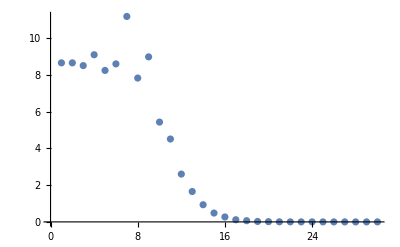

{-10 Cos[Root6.13Root[{10 Cos[10 Sin[#1]] Cos[#1]^2-Sin[10 Sin[#1]] Sin[#1]&,6.1270655027312168001}]6.127065502731217] Sin[10 Sin[Root6.13Root[{10 Cos[10 Sin[#1]] Cos[#1]^2-Sin[10 Sin[#1]] Sin[#1]&,6.1270655027312168001}]6.127065502731217]],-10 Cos[Root6.13Root[{10 Cos[10 Sin[#1]] Cos[#1]^2-Sin[10 Sin[#1]] Sin[#1]&,6.1270655027312168001}]6.127065502731217] Sin[10 Sin[Root6.13Root[{10 Cos[10 Sin[#1]] Cos[#1]^2-Sin[10 Sin[#1]] Sin[#1]&,6.1270655027312168001}]6.127065502731217]],9.82725,10.1902,9.71816,12.664,29.5418,11.4958,36.8283,12.9139,23.5842,9.5772,10.3305,4.45567,3.47557,0.357988,0.956944,0.43438,0.224426,0.103179,0.0460794,0.021376,0.00109593,0.00394593,0.00140491,0.000659418,0.000214306,0.000100993,0.0000302763,0.0000143146}

-Graphics-

```mathematica
dobr3=Table[Show[Plot[Evaluate[D[pn3[[n]],x]],{x,-1,1}],Plot[f3'[x],{x,-1,1}], PlotRange->All],{n,1,nmax}];
Manipulate[dobr3[[n]],{n,1,nmax,1},SaveDefinitions->True]
norm2d3=Table[Sqrt[NIntegrate[(f3'[x]-D[pn3[[n]],x])^2,{x,-1,1}]],{n,1,nmax}]
ListPlot[norm2d3]
normmf3=Table[Abs[MaxValue[{Simplify[f3'[x]-D[pn3[[n]],x]],-1<=x<=1},x]],{n,1,nmax}]
ListLogPlot[normmf3]
```